```mathematica
fMS[kappa_,theta_]:=Exp[kappa*Cos[theta]^2]/((√π Erfi[√kappa])/(2*√kappa))
```

```mathematica
Integrate[fMS[kappa,theta]*Sin[theta],{theta,0,Pi/2}]
```

1

```mathematica
fONSAGER[kappa_,theta_]:=Cosh[kappa*Cos[theta]]/(Sinh[kappa]/kappa)
```

```mathematica
Integrate[fONSAGER[kappa,theta]*Sin[theta],{theta,0,Pi/2}]
```

1

```mathematica
IMS[kappa_,psi_]:=Integrate[fMS[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2},Assumptions->psi≥0 && psi≤Pi/2]
```

```mathematica
IMS[kappa,psi]
```

ConditionalExpression[(ⅇ^(kappa Cos[psi]^2) √π Erf[√kappa Cos[psi]] Sec[psi])/(2 √kappa),psi>0&&2 psi<π]

```mathematica
FullSimplify[(ⅇ^(kappa Cos[psi]^2) √π Erf[√kappa Cos[psi]] Sec[psi])/(2 √kappa)/((√π Erfi[√kappa])/(√kappa))]
```

(ⅇ^(kappa Cos[psi]^2) Erf[√kappa Cos[psi]] Sec[psi])/(2 Erfi[√kappa])

```mathematica
IONSAGER[kappa_,psi_]:=Integrate[fONSAGER[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2},Assumptions->psi≥0 && psi≤Pi/2]
```

```mathematica
IONSAGER[kappa,psi]
```

Integrate[(Cosh[kappa Cos[theta]] Sec[psi]^2 Sin[theta])/(√(-Tan[psi]^2+Tan[theta]^2)),{theta,psi,π/2},Assumptions→psi≥0&&psi≤π/2]

```mathematica
IMScorr[kappa_,psi_]:=Integrate[fMS[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
IMScorr[kappa,psi]
```

∫_psi^(π/2) (fMS[kappa,theta] Sec[psi] Tan[theta])/(√(-Tan[psi]^2+Tan[theta]^2))ⅆtheta

```mathematica
IONSAGERcorr[kappa_,psi_]:=Integrate[fONSAGER[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
IONSAGERcorr[kappa,psi]
```

∫_psi^(π/2) (Cosh[kappa Cos[theta]] Sec[psi] Tan[theta])/(√(-Tan[psi]^2+Tan[theta]^2))ⅆtheta

```mathematica
NIMS[kappa_,psi_]:=NIntegrate[fMS[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
NIONSAGER[kappa_,psi_]:=NIntegrate[fONSAGER[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
NIMScorr[kappa_,psi_]:=NIntegrate[fMS[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
NIONSAGERcorr[kappa_,psi_]:=NIntegrate[fONSAGER[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
NONSAGERcorr[kappa_]:= NIntegrate[NIONSAGERcorr[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NMS[kappa_]:= NIntegrate[NIMS[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NMScorr[kappa_]:= NIntegrate[NIMScorr[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NONSAGER[kappa_]:= NIntegrate[NIONSAGER[kappa,psi],{psi,0,Pi/2}]
```

```mathematica
NONSAGER[-3]
```

NIntegrate::nlim: theta = psi is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.785398

```mathematica
NMS[2]*2/Pi
```

NIntegrate::nlim: theta = psi is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.

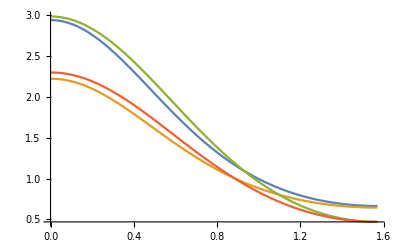

```mathematica
Plot[{NIMS[2,psi]*Pi/2,NIMScorr[2,psi]/1.03,1*NIONSAGER[-3,psi]*Pi/2,1*NIONSAGERcorr[-3,psi]},{psi,0,Pi/2}]
```

```mathematica
fSHRINK[lambda_,theta_]:=1/2*lambda^2*Cos[ArcTan[lambda*Tan[theta]]]^3/Cos[theta]^3
```

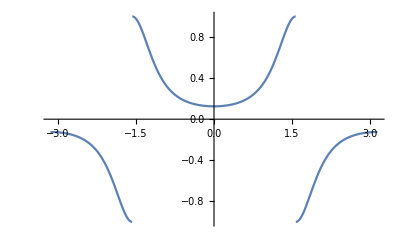

```mathematica
Plot[fSHRINK[.5,theta],{theta,-Pi,Pi}]
```